For this non-linear example, we use the following model:

First, we define the parameters:

```mathematica
S=5;
M=2;
```

```mathematica
τ=1;
μ={{2,0.5},{0.5,2},{1.5,1.5},{0.9,0.7},{0.7,0.9}};
k=μ+Table[0.1RandomReal[{-1,1}],{i,1,S},{β,1,M}];
w=Table[1+0 RandomReal[{-1,1}],{β,1,M}];
m={1,1,1.1,1,1};
e=Table[1,{i,1,S}];
```

Next, define the growth rate:

```mathematica
g[{R1_,R2_}]=e(Table[Sum[(μ[[i,α]]{R1,R2}[[α]])/(k[[i,α]]+{R1,R2}[[α]]),{α,1,M}],{i,1,S}]-m);
```

And some color-coding!

```mathematica
colors=ColorData[58]/@Range[1,S]
```

{RGBColor[0.742077, 0.0624857, 0.00605783],RGBColor[0, 0.501961, 0],RGBColor[0.891279, 0.721172, 0.777905],RGBColor[0.0620432, 0.521904, 0.704387],RGBColor[0.823529, 0.663981, 0.00828565]}

Next, we construct the infeasible region: if  belongs to the interior of the infeasible region, then no species survive.

```mathematica
ifr=Show[{ContourPlot[Evaluate@Thread[g[{R1,R2}]==0],{R1,0,5},{R2,0,5},ContourStyle->colors,ContourLabels->None,PlotTheme->"Scientific"],RegionPlot[And@@Thread[g[{R1,R2}]<=0],{R1,0,5},{R2,0,5},BoundaryStyle->None]}];
```

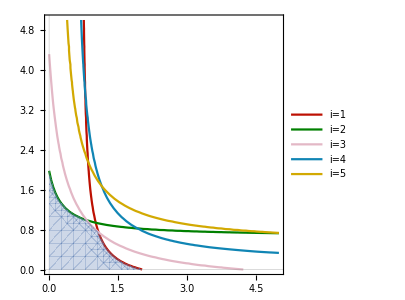

```mathematica
Legended[Show[ifr,FrameLabel->{"",""}],Placed[LineLegend[colors,(Style["i="<>ToString[#],FontFamily->"CMU Serif"])&/@Range[1,S]],{0.86,0.75}]]
```

Next, we define an optimization function, following the “Minimum Environmental Perturbation Principle” (https://arxiv.org/abs/1901.09673v4)

```mathematica
Q[{R01_,R02_},{R1_,R2_}]=τ^-1 Sum[{R01,R02}[[α]](1/({R01,R02}[[α]])Log[(1/({R01,R02}[[α]]))/(1/({R1,R2}[[α]]))]-(1/({R01,R02}[[α]])-1/({R1,R2}[[α]]))),{α,1,M}];
```

```mathematica
meppOpt[{R01_,R02_},tol_]:={{R1,R2},Thread[Abs[g[{R1,R2}]]<tol]}/.Last@FindMinimum[{Re@Q[{R01,R02},{R1,R2}],g[{R1,R2}]\[VectorLessEqual]0},{{R1,R01},{R2,R02}},Method->"InteriorPoint",PerformanceGoal->"Speed"];
meppOpt[{R01_,R02_}]:=meppOpt[{R01,R02},10^-6.];
```

Next, we define the consumption vectors for the nonlinear growth rates

```mathematica
derivcomp=FullSimplify[Table[(#[[i]].{R1,R2}-g[{R1,R2}][[i]])^-1#[[i]],{i,1,S}]&[D[g[{R1,R2}],{{R1,R2}}]]];
```

```mathematica
consumpVecs[{R1star_,R2star_}]=derivcomp/.Thread[{R1,R2}->{R1star,R2star}];
```

```mathematica
coexistencecone[solval_]:= ConicHullRegion[{solval[[1]]},τ Table[solval[[1]]^2(e[[i]] μ[[i,;;]] k[[i,;;]])/( k[[i,;;]]+solval[[1]])^2,{i,Flatten@Position[solval[[2]],True]}]]
```

```mathematica
addPCHvecs[c_]:=Join[c,{{Max[cᵀ[[1]]],0},{0,Max[cᵀ[[2]]]}}]
```

Here, we define the differential equations:

```mathematica
ClearAll[{NN,RR}]
```

```mathematica
NLCRMdiffEqs=Union[Thread[D[Table[Subscript[NN, i][t],{i,1,S}],t]==Table[Subscript[NN, i][t],{i,1,S}]g[{Subscript[RR, 1][t],Subscript[RR, 2][t]}]],Table[Subscript[RR, α]'[t]==τ^-1(Subscript[R0, α]-Subscript[RR, α][t])-Subscript[RR, α][t] Table[Subscript[NN, i][t],{i,1,S}].D[g[{Subscript[RR, 1][t],Subscript[RR, 2][t]}],Subscript[RR, α][t]],{α,1,2}]];
```

```mathematica
NLCRMdynamics=ParametricNDSolveValue[{NLCRMdiffEqs,Table[Subscript[NN, i][0]==0.05,{i,1,S}],Table[Subscript[RR, α][0]==Subscript[R0, α],{α,1,2}]},Union[Table[Subscript[NN, i][t],{i,1,S}],Table[Subscript[RR, α][t],{α,1,2}]],{t,0,100},{Subscript[R0, 1],Subscript[R0, 2]}]
```

ParametricFunction[<>]

The following will run faster because it does not numerically solve the differential equations

```mathematica
DynamicModule[{R0={1,1}},Deploy@Dynamic@Block[{solval=meppOpt[R0]},Block[{cvecs = consumpVecs[solval[[1]]]},Row[{
Column[{Show[{
ifr,
Graphics[{
Locator[Dynamic[R0]],
PointSize[Large],
Point[{solval[[1]]}],
Opacity[0.5],
Gray,
coexistencecone[solval]
}]
},ImageSize->Medium,FrameLabel->{"",""},Epilog->{PointSize[0.03],Point[5/3{2.5,2.8}],Text[Style[,FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.74,2.8}],Locator[5/3{2.5,2.6}],Text[Style["",FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.7,2.6}](*,
Text[Style[,FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.76,2.4}],
ColorData[97,"ColorList"][[1]],Thick,Line[5/3{{2.45,2.4},{2.55,2.4}}]*)
}](*,
Plot[Identity[(NLCRMdynamics@@R0)[[1;;S]]],{t,0,100},PlotRange->All,FrameLabel->{"",""},PlotStyle->colors,ImageSize->300,PlotTheme->"Scientific"]*)
}],
Show[{Graphics[{PointSize[Large],{colors,Point[#]&/@cvecs}ᵀ,Blue, Thick,Circle[#,0.025]&/@(cvecs[[Flatten@Position[(solval[[2]]),True]]]),Black,Opacity[0.1],ConvexHullRegion[addPCHvecs[cvecs]∪{{0,0}}]},PlotRange->{{0,1},{0,1}},ImageSize->Medium]
},Axes->True,AxesLabel->(Style[#,FontFamily->"CMU Serif"]&/@{"",""}),TicksStyle->Directive[FontFamily->"CMU Serif"]]
}
]]
]]
```

The following may be very slow because it both solves differential equations and performs convex optimization simultaneously:
Run the cell with some caution!

```mathematica
DynamicModule[{R0={1,1}},Deploy@Dynamic@Block[{solval=meppOpt[R0]},Block[{cvecs = consumpVecs[solval[[1]]],diffsol=(NLCRMdynamics@@R0)[[1;;S]]},Row[{
Column[{Show[{
ifr,
Graphics[{
Locator[Dynamic[R0]],
PointSize[Large],
Point[{solval[[1]]}],
Opacity[0.5],
Gray,
coexistencecone[solval]
}]
},ImageSize->Medium,FrameLabel->{"",""},Epilog->{PointSize[0.03],Point[5/3{2.5,2.8}],Text[Style[,FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.74,2.8}],Locator[5/3{2.5,2.6}],Text[Style["",FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.7,2.6}](*,
Text[Style[,FontFamily->"CMU Classical Serif",FontSize->16],5/3{2.76,2.4}],
ColorData[97,"ColorList"][[1]],Thick,Line[5/3{{2.45,2.4},{2.55,2.4}}]*)
}],
Plot[diffsol,{t,0,100},PlotRange->All,FrameLabel->{"",""},PlotStyle->colors,ImageSize->300,PlotTheme->"Scientific"]
}],
Show[{Graphics[{PointSize[Large],{colors,Point[#]&/@cvecs}ᵀ,Blue, Thick,Circle[#,0.025]&/@(cvecs[[Flatten@Position[(solval[[2]]),True]]]),Black,Opacity[0.1],ConvexHullRegion[addPCHvecs[cvecs]∪{{0,0}}]},PlotRange->{{0,1},{0,1}},ImageSize->Medium]
},Axes->True,AxesLabel->(Style[#,FontFamily->"CMU Serif"]&/@{"",""}),TicksStyle->Directive[FontFamily->"CMU Serif"]]
}
]]
]]
```